```mathematica
SetDirectory[NotebookDirectory[]<>"/../"];
<<SimulationRewardDriven4`;
SetDirectory[NotebookDirectory[]];
(*displays results of simulation*)
PlotBelief1[]:=Module[
{plot,plotforrange1,plotforrange2,data,size},
data=Table[Mean/@BELIEF[[i]],{i,1,BELIEF//Length}];
size=(Length/@data)//Max;
size=nquestionsUSER;
plot=data//ListLinePlot[#,AxesLabel->{Style["j",Large],Style["d",Large]},PlotRange->All,PlotLegends->Table[Style["a= "<>ToString[AffinityValues[[i]]]<>", b="<>ToString[BiasValues[[i]]],Large],{i,1,AffinityValues//Length}],ImageSize->Large,TicksStyle->Directive["Label", 20]]&;
plotforrange1=ListLinePlot[{Join[ConstantArray[-dMAX-0.5,size-1],ConstantArray[dMAX+0.5,1]]},ImageSize->Large,TicksStyle->Directive["Label", 20],PlotStyle->None];
Print["size=",size];
Show[plotforrange1,plot]
]

markerphase[in_:GrayLevel[0],out_:GrayLevel[0],size_:7]:=Graphics[{in,EdgeForm[{AbsoluteThickness[1],out}],Disk[]},PlotRangePadding->0,ImageSize->size]
marker[d_]:=Module[
{DMAX=dMAX,DMIN=-dMAX,opacity=0.08},
d//Which[
#==DMAX,markerphase[Opacity[opacity,ColorData["VisibleSpectrum",470]],ColorData["VisibleSpectrum",470],30*Sqrt[Abs[#]]],
#==DMIN,markerphase[Opacity[opacity,ColorData["VisibleSpectrum",630]],ColorData["VisibleSpectrum",630],30*Sqrt[Abs[#]]],
DMAX>#>0,markerphase[Transparent,ColorData["VisibleSpectrum",470],30*Sqrt[Abs[#]]],
DMIN<#<0,markerphase[Transparent,ColorData["VisibleSpectrum",630],30*Sqrt[Abs[#]]],
#==0,markerphase[Opacity[opacity,Black],Black,30],
#===666,"",
True,Style["☒",RGBColor[1, 0, 1],Large]
]&
]


marker2[{d_,reachedstopcond_}]:=Module[
{DMAX=dMAX,DMIN=-dMAX,opacity=0.2,
sizemin=6,sizeinc=3
},

d//Which[
reachedstopcond,
#//Which[
DMAX≥ #>0,markerphase[Opacity[opacity,ColorData["VisibleSpectrum",470]],ColorData["VisibleSpectrum",470],sizemin+sizeinc Sqrt[Abs[#]]],
DMIN≤ #<0,markerphase[Opacity[opacity,ColorData["VisibleSpectrum",630]],ColorData["VisibleSpectrum",630],sizemin+sizeinc Sqrt[Abs[#]]],
#==0,markerphase[Opacity[opacity,Black],Black,sizemin],
#===666,"",
True,Style["☒",RGBColor[1, 0, 1],Large]
]&,

True,
#//Which[
DMAX≥ #>0,markerphase[Transparent,ColorData["VisibleSpectrum",470],sizemin+sizeinc Sqrt[Abs[#]]],
DMIN≤ #<0,markerphase[Transparent,ColorData["VisibleSpectrum",630],sizemin+ sizeinc Sqrt[Abs[#]]],
#==0,markerphase[Transparent,Black,sizemin],
#===666,"",
True,Style["☒",RGBColor[1, 0, 1],Large]
]&

]&
]

PhasePlot[{biasaffpair_,BeliefFinal_},label_]:=Module[
{meanconclusion,markertable,invisible,range,biasaffpairPADDED,meanconclusionPADDED},
meanconclusion=Mean/@BeliefFinal;
meanconclusionPADDED=Join[{666,666},meanconclusion];
markertable=marker/@(meanconclusionPADDED);

invisible={{{bMIN,aMIN},{bMAX,aMAX}}};
range={{bMIN,bMAX},{aMIN,aMAX}};
biasaffpairPADDED=Join[invisible,List/@biasaffpair];
(*Print["plot range: ",invisible];*)

biasaffpairPADDED//ListPlot[#,PlotMarkers->markertable,PlotRange->range,ImageSize->500,LabelStyle->Directive[Bold, 16],FrameLabel->{Style["b",Bold,Large],Style["a",Bold,Large]},PlotLabel->label,PlotStyle->Thick,AspectRatio->0.9,Frame->True,ImageMargins->25]&

]

PhasePlot2[BELIEF_List,PHASE_List,label_]:=Module[
{reachedstopcond,meanconclusion,meanconclusionstop,markertable,invisible,range,range2,biasaffpair=PHASE[[1]],biasaffpairPADDED,meanconclusionstopPADDED,plot1,plot2},

Print[Style["WARNING: ",Bold,Orange,Medium]," Using nquestions=",nquestions," to verify stop condition."];

reachedstopcond=#<nquestions&/@(Length/@BELIEF);
meanconclusion=Mean/@BELIEF[[All,-1]];
meanconclusionstop={meanconclusion,reachedstopcond}//Transpose;

meanconclusionstopPADDED=Join[{{666,True},{666,True}},meanconclusionstop];
markertable=marker2/@(meanconclusionstopPADDED);
(*Print[markertable];*)



invisible={{{bMIN,aMIN}},{{bMAX,aMAX}}};
range={{bMIN,bMAX},{aMIN,aMAX}};
range2=range//Reverse;
biasaffpairPADDED=Join[invisible,List/@biasaffpair];

(*plot1=(biasaffpairPADDED)//ListPlot[#,PlotMarkers->markertable,PlotRange->range,ImageSize->500,LabelStyle->Directive[Bold, 16],FrameLabel->{Style["b",Bold,Large],Style["a",Bold,Large]},PlotLabel->label,PlotStyle->Thick,AspectRatio->0.9,Frame->True,ImageMargins->25]&;*)

plot2=(Reverse[#,2]&/@biasaffpairPADDED)//ListPlot[#,PlotMarkers->markertable,PlotRange->range2,ImageSize->500,LabelStyle->Directive[Bold, 16],FrameLabel->{Style["a",Bold,Large],Style["b",Bold,Large]},PlotLabel->label,PlotStyle->Thick,AspectRatio->0.9,Frame->True,ImageMargins->25]&;

plot2

]

GetPHASEq[qmax_]:=Module[
{length,maxlength,lengtheff,PHASEq},
length=Table[BELIEF[[i]]//Length,{i,1,BELIEF//Length}];
maxlength=Max[length];
lengtheff=Which[#≤qmax,#,True,qmax]&/@length;

If[maxlength≤qmax,
Print[Style["\nWarning: ",Orange,16,Bold],Style["requested qmax =" <>ToString[qmax]<>" is larger or equal to nqmax = "<>ToString[maxlength]<>" in simulation. No cut has been done.",16,Bold]];
];

PHASEq={PHASE[[1]],Table[BELIEF[[i,lengtheff[[i]]]],{i,1,BELIEF//Length}]}
]

indexGetBELIEFq[qnumber_,l_]:=Which[qnumber≤l,qnumber,True,-1];

GetBELIEFq[qnumber_]:=Module[
{
length=(Length/@BELIEF),
stopcondition=#<qnumber&/@length,
BELIEFq},

BELIEFq=Table[BELIEF[[i,1;;indexGetBELIEFq[qnumber,length[[i]]]]],{i,1,BELIEF//Length}]

]


INFO[]:=Module[
{info=""},
info=info<>"dinit = "<>ToString[d]<>"\n";
info=info<>"hinit = "<>ToString[h]<>"\n";
info=info<>"nquestions = "<>ToString[nquestions]<>"\n";
info=info<>"nexperiments = "<>ToString[nexperimentsUSER]<>"\n";
info=info<>"npredictors = "<>ToString[npredictors]<>"\n";
info=info<>"RTHRESHOLD = "<>ToString[RTHRESHOLD]<>"\n";
info=info<>"R0 = "<>ToString[R0]<>"\n";
info=info<>"B0 = "<>ToString[B0]<>"\n";
info=info<>INFOPREDICTIVEPOWER;

info

]


SaveSimulation[id_String]:=Module[
{dir=id,names="",out,info=""},
(*saves superarrays*)
(*names=SUPERARRAYNAME//DeleteCases["PLOTS"];
out=(Export[dir<>"/"<>#,#//ToExpression,"String"]&)/@names;
Print/@out;*)
(*saves phase space data*)
Export[dir<>"/"<>"PHASE",PHASE,"String"];
(*saves BELIEF  data*)
Export[dir<>"/"<>"BELIEF",BELIEF,"String"];
(*saves initital d, h arrays and ranges aMIN,aMAX and bMIN,bMAX, and other values for the simulation.*)
Export[dir<>"/"<>"info",INFO[],"String"];

]
LoadSimulation[id_String]:=Module[
{dir=id,names="",out,pts1,pts2,label},
(*loads superarrays*)
(*names=SUPERARRAYNAME//DeleteCases["PLOTS"]//DeleteCases["EXPERIMENT"];
names={"CREWARD"};
Unprotect/@names;
out=(#<>"=Import[\""<>dir<>"/"<>#<>"\"]//ToExpression"//ToExpression)&/@names;*)
(*loads phase space data*)
PHASE=Import[dir<>"/PHASE"]//ToExpression;
(*loads BELIEF data, WARNING: overrides current value of BELIEF*)
BELIEF//Unprotect;
BELIEF=Import[dir<>"/BELIEF"]//ToExpression;
BELIEF//Protect;
(*prints contents of info file*)
InfoCurrent=Import[dir<>"/info"];Print[InfoCurrent];
(*plot phase diagram*)
pts1=PHASE[[1]]//Length;
pts2=BELIEF//Length;
label=Which[pts1==pts2,id<>": pts = "<>ToString[pts1],True,id<>": pts1 = "<>ToString[pts1]<>",  pts2 = "<>ToString[pts2]];
PhasePlot[PHASE,label]

]

SimulationExists[id_String]:=Module[
{exists},
exists=DirectoryQ[id];
exists//TrueQ
]

(*warning: deletes current values of BELIEF, PHASE, BiasAffPair and  *)
RunSimulation[id_String,NSIMULATIONS_Integer]:=Module[
{tempplot,templine,templine0,phase,id2,fullid,IT,itregions,it,amin,amax,bmin,bmax,
check1={},
BiasAffPair={},BeliefFinal={},a,b,AffinityValues={},BiasValues={}
},

For[IT=1,IT≤NSIMULATIONS,IT++,
SeedRandom[];
id2=ToString[IT];
fullid=id<>"_"<>id2;
tempplot=0;
BELIEF//Unprotect;
BELIEF={};
BELIEF//Protect;
PHASE={};
BiasAffPair={};BeliefFinal={};AffinityValues={};BiasValues={};
If[SimulationExists[fullid],Print["Simulation '"<>fullid<>"' exists. Aborting."],
SaveSimulation[fullid];
For[itregions=1,itregions≤(nregions),itregions++,
(*sets range of a and b for current region*)
{{amin,amax},{bmin,bmax}}=REGION[[itregions]];
NotebookDelete[templine0];
NotebookDelete[tempplot];
templine0=PrintTemporary[Style["region=",Large,Bold],Style[itregions,Large,Bold],
Style[" (out of "<>ToString[nregions]<>")",Large,Bold]];
tempplot=PrintTemporary[phase];

For[it=1,it≤ptsREGION,it++,
(*to show progress*)
NotebookDelete[templine];
templine=PrintTemporary[Style["it=",Large,Bold],Style[it,Large,Bold]];
(*sets and stores values of a,b for all iterations*)
a=ConstantArray[RandomReal[{amin,amax}],npredictors];
b=ConstantArray[RandomReal[{bmin,bmax}],npredictors];
AppendTo[AffinityValues,a//Mean];
AppendTo[BiasValues,b//Mean];
(*initialize experiment*)
InitExperimentRewardDriven[d,a,b,h];
(*run experiment*)
RunExperimentStop[];
(*saves data on degree of belief during the simulation*)
StoreBeliefCurrent[];
(*store values for phase plot*)
BiasAffPair=Table[{BiasValues[[i]],AffinityValues[[i]]},{i,1,AffinityValues//Length}];
BeliefFinal=Table[BELIEF[[i,-1]],{i,1,BELIEF//Length}];
PHASE={BiasAffPair,BeliefFinal};
phase=PhasePlot[PHASE,"j="<>ToString[it]];
If[Mod[it,10]==0||it==1,NotebookDelete[tempplot];tempplot=PrintTemporary[phase]];

If[
Mod[it,30]==0,
SaveSimulation[fullid],
Nothing,Nothing
]

];
SaveSimulation[fullid];
(*check1*)
EXPERIMENT//Flatten//Cases[x_:>x/;!NumericQ[x]];
AppendTo[
check1,
List[Style["This should print a value of 0: value =  ",Large,Bold,Black],Style[%//Length//ToString,Bold,Large,Blue]]
];
Init[];
];
SaveSimulation[fullid]
];
check1//DeleteDuplicates//MatrixForm//Print
];
BELIEF//Unprotect;
BELIEF={};
BELIEF//Protect;
PHASE={};
]

nquestionsUSER=10;
nexperimentsUSER=10;
npredictorsUSER=20;
(*affinity related settings, keep fixed*)
RTHRESHOLD=4.04;
NSTABLE=4;
R0=50;
(*bias related settings*)
B0=0.7;
(*set forecast: dmax=4,nsteps=8, max power= 21 ⟹ max{Subscript[p, avg]} = 0.9545 , keep fixed *)
BuildPredictivePowerFunction[4,8];

(*unused but needed for function below 'InitSimulationRewardDriven'*)
a=ConstantArray[0,npredictorsUSER];(*a here means a0 in draft*)
b=ConstantArray[0,npredictorsUSER];

(*initial degree of belief and random walk parameter h*)
d={4,4,4,4,4,4,4,4,4,4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4};
h=ConstantArray[0.99,npredictorsUSER];
```

ν values = {1.,1.58824,2.66667,5.28571,21.}

ν values = {1.,1.58824,2.66667,5.28571,21.}

Initialize simulation. 
This sets up the INITIAL values for d,a,b,h which are all lists of size ‘nquestionsUSER’:
- d:  is  the degree of belief on the theory (theory is correct by construction)
- a:  the affinity or tendency for experts to change their belief on the theory, motivated by getting higher rewards.
- b:  is the bias or tendency to reject the objective outcome of experiments, based on their own belief of the theory 
- h:  random walk parameter, associated to the  probability  of experts to change their degree of belief randomly,
          Probability of Random Walk = 2h(1-h)
         examples:  h=0.5   →  50%   ,  h=0.99   →  2% ,  h=1.0   →  0% (no random walk).
The simulation performs a number of experiments given by ‘nexperimentsUSER’. Each experiment asks a number of questions given by  ‘nquestionsUSER’

```mathematica
(*set ranges for a0 and b (below, 'a' refers to 'a0' in draft).*)
aMIN=0.0;aMAX=0.25;
bMIN=0.0;bMAX=1.0;
(*divides full range in separate regions. If a diverent subdivision of regions is wanted, only quantities marked with '++++++++++' should be changed.  *)
(*++++++++++*)aINTERVALS=1;
(*++++++++++*)bINTERVALS=1;
nregions=aINTERVALS bINTERVALS;
ptsREGION=Which[nexperimentsUSER==nregions,1,nexperimentsUSER/nregions≥ 10,Round[nexperimentsUSER/nregions],True,IntegerPart[nexperimentsUSER/nregions]];
aGRID=Range[aMIN,aMAX,(aMAX-aMIN)/aINTERVALS];
bGRID=Range[bMIN,bMAX,(bMAX-bMIN)/bINTERVALS];
REGION=Table[{aGRID[[i;;i+1]],bGRID[[j;;j+1]]},{i,1,(aGRID//Length)-1},{j,1,(bGRID//Length)-1}]//Flatten[#,1]&;
(*initializes the simulation*)
InitSimulationRewardDriven[d,a,b,h];
```

Run simulation. 
This runs a ‘for-loop’, each iteration corresponds to an experiment. Each iteration generates new values for a and b, and uses the current values for 
d, updating it according to the affinity, bias and random walk.  
Arrays  ‘PHASE’ and ‘BELIEF’are saved at intermediate steps. SUPERARRAYS are not saved at the time.
WARNING: Change the “id” each simulation.

### Decide how many simulations should be run with NSIMULATIONS

```mathematica
NSIMULATIONS=5;
id="test_trash";
RunSimulation[id,NSIMULATIONS]
```

(This should print a value of 0: value =   | 0)

(This should print a value of 0: value =   | 0)

(This should print a value of 0: value =   | 0)

«2 more identical outputs»

dinit = {4, 4, 4, 4, 4, 4, 4, 4, 4, 4, -4, -4, -4, -4, -4, -4, -4, -4, -4, -4}
hinit = {0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99}
nquestions = 10
nexperiments = 10
npredictors = 20
RTHRESHOLD = 4.04
R0 = 50
B0 = 0.7
######## predictive power function genereted by calling: 'BuildPredictivePowerFunction[4,8]'
dMAX = 4
dSTEPS = 8
dSTEPSIZE = 1
forecastavgMAX = 0.954545
PowerValues = {1., 1.58824, 2.66667, 5.28571, 21.}
forecastavg = {0.0454545, 0.159091, 0.272727, 0.386364, 0.5, 0.613636, 0.727273, 0.840909, 0.954545}

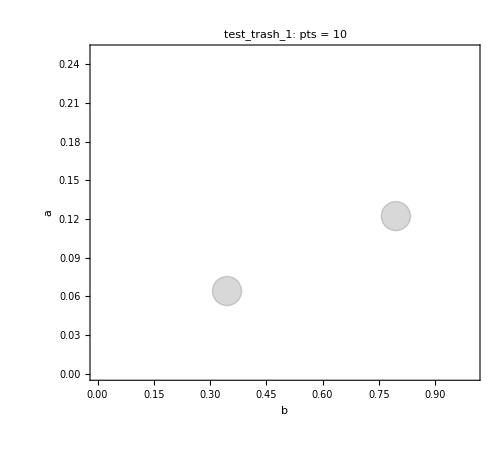

```mathematica
LoadSimulation["test_trash_1"]
```

```mathematica
BELIEF//Length
```

0

```mathematica
PHASE[[1]]//Length
```

Part::partw: Part 1 of {} does not exist.

2

True